# General Ray Tracking

General consideration
a point on a plane, the projection on a line with angle θ with x-axis is
{x,y}.{Cos[θ],Sin[θ]}
if the point is formed by a ray
{x,y}={X0+A z,Y0+B z}
thus, the lenght on that line is
P={X0+A z,Y0+B z}.{Cos[θ],Sin[θ]}
if we have many plane wiht difference z, then the respond Yi can form a matrix
Pi = {Cos[θi], Cos[θi]zi, Sin[θi], Sin[θi]zi}.{X0,A,Y0,B}
in matrix Form
P= H. β
the solution is
β=(H^T H)^-1 H^T Y = G Y
var[β]=(H^T H)^-1 σ^2 =X σ^2
where best estimator of σ^2 is
 σ^2=SSR
the residual is
e=(1-H G)Y=(1-Q)Y
var[e]=(1-Q)σ^2

```mathematica
numPlane = 6;
weight={1,1,1,1,1,1};
w=Table[KroneckerDelta[i,j]weight[[i]],{i,1,numPlane},{j,1,numPlane}];
θList={0,0 ,36.87,36.87,-36.87,-36.87};
zList={-40,-24,-8,8,24,40};
H=w.Table[ {Cos[θList[[i]] °], Cos[θList[[i]]°]zList[[i]], Sin[θList[[i]]°], Sin[θList[[i]]°]zList[[i]]},{i,1,Length[θList]}];
G = Inverse[Transpose[H].H].Transpose[H];
X = Inverse[Transpose[H].w.w.H];
Q = H.G;
(* display *)
w//MatrixForm;
{"H=",Round[H,0.001]//MatrixForm}
{"G=",Round[G,0.001]//MatrixForm}
{"var[β]=",Round[X,0.001]//MatrixForm}
{"var[e]=",Round[IdentityMatrix[Length[θList]]-Q,0.01]//MatrixForm}
Table[√((IdentityMatrix[Length[θList]]-Q)[[i,i]]),{i,1,6}]
Length[θList]-Tr[Q]
Table[X[[i,i]],{i,1,4}]
Table[√X[[i,i]],{i,1,4}]
```

{H=,(1. | -40. | 0. | 0.
1. | -24. | 0. | 0.
0.8 | -6.4 | 0.6 | -4.8
0.8 | 6.4 | 0.6 | 4.8
0.8 | 19.2 | -0.6 | -14.4
0.8 | 32. | -0.6 | -24.)}

{G=,(0.077 | 0.366 | -0.29 | 0.638 | 0.407 | -0.059
-0.014 | -0.001 | -0.01 | 0.02 | 0.01 | 0.
-0.144 | -0.396 | 1.182 | -0.011 | -0.642 | 0.147
-0.01 | 0.023 | -0.061 | 0.054 | 0.027 | -0.035)}

{var[β]=,(0.799 | 0.018 | -0.775 | 0.073
0.018 | 0.001 | -0.016 | 0.002
-0.775 | -0.016 | 2.01 | -0.103
0.073 | 0.002 | -0.103 | 0.009)}

{var[e]=,(0.35 | -0.42 | -0.12 | 0.17 | -0.02 | 0.07
-0.42 | 0.6 | 0.05 | -0.16 | -0.17 | 0.06
-0.12 | 0.05 | 0.16 | -0.12 | 0.25 | -0.21
0.17 | -0.16 | -0.12 | 0.11 | -0.13 | 0.12
-0.02 | -0.17 | 0.25 | -0.13 | 0.49 | -0.37
0.07 | 0.06 | -0.21 | 0.12 | -0.37 | 0.29)}

{0.58738,0.774162,0.403221,0.333062,0.70171,0.538278}

2.

{0.79903,0.000812316,2.00963,0.00921222}

{0.893885,0.0285012,1.41761,0.0959803}

```mathematica
G//MatrixForm
G5[[3]]//MatrixForm
```

(-0.131365 | 0.447047 | 0. | 0.427699 | 0.855397 | -0.427699
-0.0217668 | 0.0014002 | 0. | 0.0127291 | 0.0254582 | -0.0127291
0.7074 | -0.727766 | 0. | 0.846062 | -2.47454 | 1.65394
-0.0544807 | 0.0400543 | 0. | 0.00901646 | 0.1222 | -0.113183)

(-0.131365 | 0.447047 | 0.427699 | 0.855397 | -0.427699
-0.0217668 | 0.0014002 | 0.0127291 | 0.0254582 | -0.0127291
0.7074 | -0.727766 | 0.846062 | -2.47454 | 1.65394
-0.0544807 | 0.0400543 | 0.00901646 | 0.1222 | -0.113183)

```mathematica
Q//MatrixForm
Q5[[3]]//MatrixForm
```

(0.739308 | 0.391039 | 0. | -0.0814664 | -0.162933 | 0.0814664
0.391039 | 0.413442 | 0. | 0.1222 | 0.244399 | -0.1222
0. | 0. | 0. | 0. | 0. | 0.
-0.0814664 | 0.1222 | 0. | 0.974542 | -0.0509165 | 0.0254582
-0.162933 | 0.244399 | 0. | -0.0509165 | 0.898167 | 0.0509165
0.0814664 | -0.1222 | 0. | 0.0254582 | 0.0509165 | 0.974542)

(0.739308 | 0.391039 | -0.0814664 | -0.162933 | 0.0814664
0.391039 | 0.413442 | 0.1222 | 0.244399 | -0.1222
0. | 0. | 0. | 0. | 0.
-0.0814664 | 0.1222 | 0.974542 | -0.0509165 | 0.0254582
-0.162933 | 0.244399 | -0.0509165 | 0.898167 | 0.0509165
0.0814664 | -0.1222 | 0.0254582 | 0.0509165 | 0.974542)

```mathematica
Plane5ID2=Table[ReplacePart[{1,2,3,4,5,6},{7-i}->0],{i,1,6}];
m5=Table[
 Table[
If[Plane5ID2[[k,i]]≠ 0,Drop[IdentityMatrix[6][[Plane5ID2[[k,i]]]],{k}],{0,0,0,0,0}],{i,1,6}]
,{k,1,6}];
```

```mathematica
Plane5ID=Table[Drop[{1,2,3,4,5,6},{i}],{i,1,6}]
H5=Table[ {Cos[θList[[Plane5ID[[k,i]]]] °],
 Cos[θList[[Plane5ID[[k,i]]]]°]zList[[Plane5ID[[k,i]]]],
 Sin[θList[[Plane5ID[[k,i]]]]°],
 Sin[θList[[Plane5ID[[k,i]]]]°]zList[[Plane5ID[[k,i]]]]}
,{k,1,6},{i,1,Length[Plane5ID[[k]]]}];
G5 = Table[Inverse[Transpose[H5[[k]]].H5[[k]]].Transpose[H5[[k]]],{k,1,6}];
Q5 = Table[H.G5[[k]],{k,1,6}];
X5 = Table[Inverse[Transpose[H5[[k]]].H5[[k]]],{k,1,6}];
varK5=Table[Q5[[k]].IdentityMatrix[5].Transpose[Q5[[k]]],{k,1,6}];
covarK5=Table[H.G.m5[[k]].Transpose[H.G5[[k]]],{k,1,6}];
(* display *)
Round[H5[[1]],0.001]//MatrixForm
Round[G5[[1]],0.001]//MatrixForm
Table[√(Q[[k,k]]+varK5[[k,k,k]]-2covarK5[[k,k,k]]),{k,1,6}]
Transpose[Table[√X5[[k,i,i]],{k,1,6},{i,1,4}]]//TableForm
```

{{2,3,4,5,6},{1,3,4,5,6},{1,2,4,5,6},{1,2,3,5,6},{1,2,3,4,6},{1,2,3,4,5}}

(1. | -24. | 0. | 0.
0.8 | -6.4 | 0.6 | -4.8
0.8 | 6.4 | 0.6 | 4.8
0.8 | 19.2 | -0.6 | -14.4
0.8 | 32. | -0.6 | -24.)

(0.461 | -0.263 | 0.6 | 0.411 | -0.074
-0.019 | -0.015 | 0.027 | 0.009 | 0.003
-0.573 | 1.133 | 0.058 | -0.65 | 0.175
0.01 | -0.065 | 0.058 | 0.026 | -0.033)

{1.12698,0.607159,2.11756,2.71591,0.803704,1.33148}

0.903483 | 1.01115 | 1.14659 | 2.11286 | 1.06529 | 0.900476
0.0376451 | 0.0285625 | 0.0380518 | 0.0667405 | 0.0316779 | 0.0285044
1.43864 | 1.50729 | 3.25649 | 1.418 | 1.68748 | 1.4436
0.0975586 | 0.100416 | 0.179992 | 0.187204 | 0.103428 | 0.115834

```mathematica
Table[Round[100(Q+varK5[[k]]-2covarK5[[k]]),1]/100//N//MatrixForm,{k,1,6}]
```

{(1.27 | 0.82 | 0.2 | -0.3 | -0.01 | -0.23
0.83 | 0.54 | 0.12 | -0.19 | -0.02 | -0.18
0.14 | 0.08 | 0.12 | -0.09 | 0.16 | 0.28
-0.27 | -0.17 | -0.1 | 0.1 | -0.1 | -0.15
-0.11 | -0.09 | 0.14 | -0.08 | 0.28 | 0.53
-0.41 | -0.29 | 0.24 | -0.1 | 0.52 | 1.04),(0.3 | 0.29 | -0.04 | 0.12 | 0.14 | -0.03
0.33 | 0.37 | -0.12 | 0.17 | 0.31 | 0.08
-0.1 | -0.18 | 0.14 | -0.1 | -0.29 | -0.17
0.15 | 0.18 | -0.08 | 0.09 | 0.19 | 0.08
0.27 | 0.41 | -0.28 | 0.22 | 0.62 | 0.34
0.06 | 0.17 | -0.19 | 0.12 | 0.4 | 0.27),(0.11 | -0.07 | 0.36 | -0.24 | -0.16 | 0.14
-0.06 | 0.05 | -0.01 | 0.27 | 0.05 | -0.05
0.58 | -0.21 | 4.48 | 0.84 | -1.31 | 1.07
-0.06 | 0.18 | 1.9 | 1.82 | -0.27 | 0.2
-0.2 | 0.1 | -1.11 | 0.07 | 0.38 | -0.31
0.17 | -0.09 | 0.89 | -0.09 | -0.31 | 0.26),(0.24 | -0.2 | 0.05 | -1.08 | -0.22 | 0.2
-0.23 | 0.21 | 0.08 | 1.15 | 0.19 | -0.18
-0.28 | 0.36 | 1.74 | 2.72 | -0.05 | -0.01
-1.35 | 1.27 | 1.17 | 7.38 | 1.03 | -0.98
-0.17 | 0.12 | -0.35 | 0.52 | 0.21 | -0.19
0.16 | -0.13 | 0.27 | -0.56 | -0.19 | 0.17),(0.37 | 0.4 | -0.12 | 0.18 | 0.32 | 0.07
0.35 | 0.43 | -0.2 | 0.21 | 0.46 | 0.19
-0.05 | -0.13 | 0.14 | -0.09 | -0.29 | -0.2
0.14 | 0.19 | -0.11 | 0.1 | 0.25 | 0.12
0.17 | 0.34 | -0.31 | 0.21 | 0.65 | 0.41
-0.04 | 0.07 | -0.17 | 0.07 | 0.34 | 0.27),(0.89 | 0.59 | 0.04 | -0.15 | -0.18 | -0.47
0.58 | 0.39 | 0.01 | -0.09 | -0.14 | -0.36
0.11 | 0.06 | 0.16 | -0.12 | 0.25 | 0.45
-0.19 | -0.12 | -0.11 | 0.1 | -0.14 | -0.23
-0.06 | -0.07 | 0.27 | -0.17 | 0.48 | 0.9
-0.26 | -0.22 | 0.5 | -0.29 | 0.92 | 1.77)}

```mathematica
Table[Round[Q[[k,k]]+varK5[[k,k,k]]-2covarK5[[k,k,k]],0.01],{k,1,6}]
Table[Round[100 √(Q[[k,k]]+varK5[[k,k,k]]-2covarK5[[k,k,k]]),1]/100//N,{k,1,6}]
```

{1.27,0.37,4.48,7.38,0.65,1.77}

{1.13,0.61,2.12,2.72,0.8,1.33}

```mathematica
LinearModelFit[{X,{1,1,1,1,1,1}}]["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
#1 | 1 | 5.92982 | 5.92982 | 1963.55 | 0.000508892
#2 | 1 | 0.0513675 | 0.0513675 | 17.0094 | 0.0540672
#3 | 1 | 0.0116939 | 0.0116939 | 3.87221 | 0.187958
#4 | 1 | 0.00107421 | 0.00107421 | 0.355705 | 0.611416
Error | 2 | 0.0060399 | 0.00301995 |  | 
Total | 6 | 6. |  |  |

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
FRatioPValue[17.00938744517648,1,2]
```

OneSidedPValue→0.0540672

```mathematica
InverseCDF[FRatioDistribution[3,1],0.95]
```

215.707

```mathematica
InverseCDF[FRatioDistribution[3,2],0.95]
```

19.1643

```mathematica
InverseCDF[FRatioDistribution[1,4],0.95]
```

7.70865

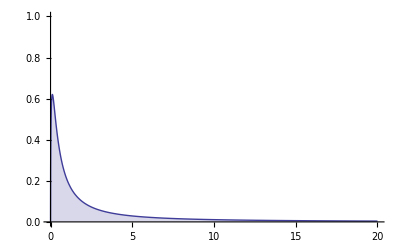

```mathematica
Plot[Evaluate[PDF[FRatioDistribution[3,1],x]],{x,0,20},PlotRange->{0,1},Filling->Axis,Exclusions->None]
```

## Constructing the 3 D model of MWDC

```mathematica
cellList={9,9,9,9,9,9,9};
celldepht={9,9,9,9,9,9,9};
cellHight={144,144,144,144,144,144,144};
centerList(* cell *)={-12.5,-12,-12.5,-13,-12.5,-12.5,-8.5};
wireNum={24,24,24,24,24,24,16};
wstartX=Table[cellList[[i]]/Cos[θList[[i]]°] centerList[[i]],{i,1,Length[θList]}]
wPos[plane_,i_]:={wstartX[[plane]]+i cellList[[plane]]/Cos[θList[[plane]]°],0,zList[[plane]]}
cell[plane_]:={cellList[[plane]],cellHight[[plane]]/Cos[θList[[plane]]°],celldepht[[plane]]}
```

{-129.904,-72 √3,-129.904,-78 √3,-112.5,-129.904,-108.187}

```mathematica
Graphics3D[{
Cylinder[{{0,0,0},{0,0,1}},7],
Arrow[{wPos[1,1],wPos[1,1]+{100,0,0}}],
Arrow[{{0,0,-900},{0,0,10}}],
Arrow[{wPos[1,1],wPos[1,1]+{0,1/2 cellHight[[1]],0}}],
Arrow[{wPos[1,1]-{0,0,100},wPos[1,1]+{0,0,100}}],
Table[
{Hue[(j-1)/Length[θList]],Opacity[1],EdgeForm[Opacity[1]],
Rotate[Cuboid[wPos[j,i]+1/2 cell[j],wPos[j,i]-1/2 cell[j]],θList[[j]]°,{0,0,1},wPos[j,i]]}
,{j,1,Length[θList]},{i,1,wireNum[[j]]}]
},ImageSize->900]
```

-Graphics3D-

```mathematica
Graphics3D[{
Arrow[{wPos[5,1],wPos[5,1]+{100,0,0}}],
Arrow[{wPos[5,1],wPos[5,1]+{0,1/2 cellHight[[1]],0}}],
Arrow[{wPos[5,1]-{0,0,100},wPos[5,1]+{0,0,100}}],
Table[
{Hue[(j-1)/Length[θList]],Opacity[0.5],EdgeForm[Opacity[1]],
Rotate[Cuboid[wPos[j,i]+1/2 cell[j],wPos[j,i]-1/2 cell[j]],θList[[j]]°,{0,0,1},wPos[j,i]]}
,{j,5,Length[θList]},{i,1,wireNum[[j]]}]
},ImageSize->800]
```

-Graphics3D-

## Tpla + MWDC Tracking

```mathematica
weight={1,1,1,1,1,1,0};
w=Table[KroneckerDelta[i,j]weight[[i]],{i,1,7},{j,1,7}];
θList={0,0,ArcCos[0.8] 180/π,ArcCos[0.8] 180/π,-ArcCos[0.8] 180/π,-ArcCos[0.8] 180/π,0};
zList={-40,-24,-8,8,24,40,1400-1022.37};
H=w.Table[ {Cos[θList[[i]] °], Cos[θList[[i]]°]zList[[i]], Sin[θList[[i]]°], Sin[θList[[i]]°]zList[[i]]},{i,1,Length[θList]}];
G = Inverse[Transpose[H].H].Transpose[H];
X = Inverse[Transpose[H].w.w.H];
Q = H.G;
(* display *)
w//MatrixForm;
{"H=",Round[H,0.001]//MatrixForm}
{"G=",Round[G 10000,1]/10000//N//MatrixForm}
(*Round[X,0.001]//MatrixForm
Round[IdentityMatrix[Length[θList]]-Q,0.01]//MatrixForm
Table[√((IdentityMatrix[Length[θList]]-Q)[[i,i]]),{i,1,6}]
Length[θList]-Tr[Q]
Table[√X[[i,i]],{i,1,4}]*)
```

{H=,(1. | -40. | 0. | 0.
1. | -24. | 0. | 0.
0.8 | -6.4 | 0.6 | -4.8
0.8 | 6.4 | 0.6 | 4.8
0.8 | 19.2 | -0.6 | -14.4
0.8 | 32. | -0.6 | -24.
0. | 0. | 0. | 0.)}

{G=,(0.0772 | 0.3659 | -0.2895 | 0.6376 | 0.4066 | -0.0585 | 0.
-0.0144 | -0.0014 | -0.0102 | 0.0201 | 0.0097 | 0.0002 | 0.
-0.1439 | -0.3965 | 1.1821 | -0.011 | -0.6423 | 0.1468 | 0.
-0.0103 | 0.0228 | -0.0614 | 0.0535 | 0.027 | -0.0349 | 0.)}

```mathematica
G.p
H[[7]]
```

{-549.297,-0.692473,35.4805,-1.45661}

{0.001,0.37763,0.,0.}

```mathematica
pp={-521.33,-533.08,0,-429.49,-452.88,-448.01,-727.624};
p=w.pp;
Round[G.p 100,1]/100//N
Round[H.G.p 1000,1]/1000//N
LinearModelFit[{H,p}]["ParameterTable"]
Round[Table[If[w[[i,i]]==0,0,(LinearModelFit[{H,p}]["PredictedResponse"])[[i]]/w[[i,i]]],{i,1,7}]100,1]/100//N
```

{-549.3,-0.69,35.48,-1.46}

{-521.599,-532.678,0.,-429.573,-453.047,-447.927,-0.811}

| Estimate | Standard Error | t-Statistic | P-Value
#1 | -549.297 | 0.351599 | -1562.28 | 5.78348×10^-10
#2 | -0.692473 | 0.0116681 | -59.3474 | 0.0000105395
#3 | 35.4805 | 0.998618 | 35.5296 | 0.0000490303
#4 | -1.45661 | 0.0551938 | -26.3909 | 0.000119363

{-521.6,-532.68,0.,-429.57,-453.05,-447.93,-810.8}

```mathematica
planeID
```

{1,2,3,4,0,0}

```mathematica
Table[
planeID=Table[If[k==ii || k == jj,0,k],{k,1,6}];
numPlane = 6-Count[planeID, 0];
If[numPlane == 6, missing=7,
If[numPlane == 5, missing=21;Do[missing=missing-planeID[[i]],{i,1,6}],
If[numPlane==4,
Len=91;
Do[Len=Len-planeID[[i]]^2,{i,1,6}];
Do[Do[(*Print[{i,j,i^2+j^2,Len}]*)If[Len== i^2+j^2,missing=10i+j;],{j,i+1,6}],{i,1,5}],missing=-1]]];
{planeID,numPlane,missing},{ii,1,5},{jj,ii+1,6}]
```

{{{{0,0,3,4,5,6},4,12},{{0,2,0,4,5,6},4,13},{{0,2,3,0,5,6},4,14},{{0,2,3,4,0,6},4,15},{{0,2,3,4,5,0},4,16}},{{{1,0,0,4,5,6},4,23},{{1,0,3,0,5,6},4,24},{{1,0,3,4,0,6},4,25},{{1,0,3,4,5,0},4,26}},{{{1,2,0,0,5,6},4,34},{{1,2,0,4,0,6},4,35},{{1,2,0,4,5,0},4,36}},{{{1,2,3,0,0,6},4,45},{{1,2,3,0,5,0},4,46}},{{{1,2,3,4,0,0},4,56}}}

```mathematica
Table[
planeID=Table[If[k==ii || k == jj,0,k],{k,1,6}];
numPlane = 6-Count[planeID, 0];
If[numPlane == 6, missing=7,
If[numPlane == 5,Do[If[planeID[[i]]== 0,missing=i],{i,1,6}],
If[numPlane==4,
Do[Do[(*Print[{i,j,i^2+j^2,Len}]*)If[planeID[[i]]==0 && planeID[[j]]==0,missing=10i+j;],{j,i+1,6}],{i,1,5}],missing=-1]]];
{planeID,numPlane,missing},{ii,1,5},{jj,ii+1,6}]
```

{{{{0,0,3,4,5,6},4,12},{{0,2,0,4,5,6},4,13},{{0,2,3,0,5,6},4,14},{{0,2,3,4,0,6},4,15},{{0,2,3,4,5,0},4,16}},{{{1,0,0,4,5,6},4,23},{{1,0,3,0,5,6},4,24},{{1,0,3,4,0,6},4,25},{{1,0,3,4,5,0},4,26}},{{{1,2,0,0,5,6},4,34},{{1,2,0,4,0,6},4,35},{{1,2,0,4,5,0},4,36}},{{{1,2,3,0,0,6},4,45},{{1,2,3,0,5,0},4,46}},{{{1,2,3,4,0,0},4,56}}}

## Fixed point Linear Regression

```mathematica
(* General consideration *)
(* a point on a plane, the projection on a line with angle θ with x-axis is *)
{x,y}.{Cos[θ],Sin[θ]}
(* if the point is formed by a ray *)
{x,y}={X0+A z,Y0+B z}
(* if the ray pass thought the point (xo, yo, zo) *)
{xo,yo}={X0+A(zo),Y0+B(zo)}
(*thus *)
{x,y}={(1-z/zo)X0+ xo/zo z,(1-z/zo)Y0+yo/zo z}
(* thus, the lenght on that line is *)
Y={(1-z/zo)X0+ xo/zo z,(1-z/zo)Y0+yo/zo z}.{Cos[θ],Sin[θ]}
(* if we have many plane wiht difference z, then the respond Yi can form a matrix *)
Yi = {Cos[θi](1-zi/zo),  Sin[θi](1-zi/zo), Cos[θi] xo/zo zi+Sin[θi] yo/zo zi}.{X0,Y0,1}
(*usually, we will defined some point that {xo,yo}={0,0} *)
Yi = {Cos[θi](1-zi/zo),  Sin[θi](1-zi/zo)}.{X0,Y0}
(* in matrix Form *)
Y= X. β
(* the solution is *)
β=(X^T X)^-1 X^T Y = G Y
var[β]=(X^T X)^-1 σ^2 =H Y
(* where best estimator of σ^2 is *)
 σ^2=SSR
(* the residual is *)
e=(1-X(X^T X)^-1)Y=(1-P)Y
var[e]=(1-P)σ^2
```

```mathematica
θListf={0,0,ArcCos[0.8] 180/π,ArcCos[0.8] 180/π,-ArcCos[0.8] 180/π,-ArcCos[0.8] 180/π};
zListf={-40,-24,-8,8,24,40};
zf=-1022.37;
Xf=Table[ {Cos[θListf[[i]] °](1-zListf[[i]]/zf),  Sin[θListf[[i]]°](1-zListf[[i]]/zf)},{i,1,Length[θListf]}];
Gf = Inverse[Transpose[Xf].Xf].Transpose[Xf];
Hf = Inverse[Transpose[Xf].Xf];
Pf = Xf.Inverse[Transpose[Xf].Xf].Transpose[Xf];
(* display *)
{"Xf ",Round[Xf,0.001]//MatrixForm}
{"Gf",Round[Gf,0.001]//MatrixForm}
{"Hf",Hf//MatrixForm}
Round[IdentityMatrix[Length[θListf]]-Pf,0.001]//MatrixForm
Length[θListf]-Tr[Pf]
Table[√Hf[[i,i]],{i,1,2}]
```

{Xf ,(0.961 | 0.
0.977 | 0.
0.794 | 0.595
0.806 | 0.605
0.819 | -0.614
0.831 | -0.623)}

{Gf,(0.213 | 0.216 | 0.181 | 0.184 | 0.176 | 0.178
0.009 | 0.009 | 0.408 | 0.415 | -0.406 | -0.412)}

{Hf,(0.221439 | 0.00909624
0.00909624 | 0.673382)}

(0.796 | -0.208 | -0.174 | -0.177 | -0.169 | -0.171
-0.208 | 0.789 | -0.177 | -0.18 | -0.172 | -0.174
-0.174 | -0.177 | 0.613 | -0.393 | 0.102 | 0.104
-0.177 | -0.18 | -0.393 | 0.601 | 0.104 | 0.105
-0.169 | -0.172 | 0.102 | 0.104 | 0.607 | -0.399
-0.171 | -0.174 | 0.104 | 0.105 | -0.399 | 0.595)

4.

{0.470573,0.820599}

```mathematica
LinearModelFit[{Xf,{1,2,3,4,5,6}}]["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
#1 | 1 | 68.2507 | 68.2507 | 14.4174 | 0.0191526
#2 | 1 | 3.81375 | 3.81375 | 0.805626 | 0.420158
Error | 4 | 18.9356 | 4.7339 |  | 
Total | 6 | 91. |  |  |

```mathematica
FRatioPValue[14.417,1,4]
```

OneSidedPValue→0.0191535

```mathematica
InverseCDF[FRatioDistribution[1,4],0.95]
```

7.70865

```mathematica
InverseCDF[FRatioDistribution[1,3],0.95]
```

10.128